## Resavanje j-na za sistem od 4 nivoa

```mathematica
Clear[Δp]
(*Δp=0;*)

γ1=1;
γ2=1;
γp=1;
γc=1;

Δc=0;
Δ1=0;
Δ2=Δp+Δc-Δ1;

Ωc0=10;
Ωp0=0.05;
Ω10=10;
Ω20=1;

ϕ=0;

S=Solve[{
(* 1 1 *)  γp σ22+γ2 σ44+ⅈ Ω20(σ41-σ14)+ⅈ Ωp0( σ21-σ12)==0,
(* 1 2 *) -(1/2 γp-ⅈ Δp)σ12-ⅈ (σ11-σ22)Ωp0+ⅈ ⅇ^(-ⅈ ϕ)Ω20 σ42-ⅈ ⅇ^(-ⅈ ϕ)Ωc0 σ13==0,
(* 1 3 *) -(1/2(γ1+γc)-ⅈ (Δ1+Δ2)) σ13- ⅈ ⅇ^(ⅈ ϕ)(Ωc0 σ12-Ωp0 σ23)+ⅈ (Ω20 σ43-Ω10 σ14)==0,
(* 1 4 *) -(1/2 γ2-ⅈ Δ2)σ14-ⅈ Ω20(σ11-σ44)+ⅈ ⅇ^(ⅈ ϕ) σ24 Ωp0-ⅈ Ω10 σ13==0,


(* 2 1 *) -(1/2 γp+ⅈ Δp)σ21-ⅈ ⅇ^(ⅈ ϕ)(σ24 Ω20-σ31 Ωc0)-ⅈ(σ22-σ11) Ωp0==0,
(* 2 2 *) -γp σ22+γc σ33+ⅈ Ωc0(σ32-σ23)+ⅈ Ωp0(σ12-σ21)==0,
(* 2 3 *) -(1/2(γ1+γc+γp)-ⅈ Δc)σ23-ⅈ σ24 Ω10-ⅈ Ωc0(σ22-σ33)+ⅈ ⅇ^(-ⅈ ϕ) Ωp0 σ13==0,
(* 2 4 *) -(1/2(γ2+γp)+ⅈ(Δp-Δ2))σ24-ⅈ ⅇ^(-ⅈ ϕ)σ21 Ω20+ⅈ σ34 Ωc0-ⅈ Ω10 σ23+ⅈ ⅇ^(-ⅈ ϕ) Ωp0 σ14==0,

(* 3 1 *) -(1/2(γ1+γc)+ⅈ (Δ1+Δ2))σ31+ⅈ σ41 Ω10-ⅈ σ34 Ω20+ⅈ ⅇ^(ⅈ ϕ)(σ21 Ωc0-σ32 Ωp0)==0,
(* 3 2 *) - (1/2(γ1+γc+γp)+ⅈ Δc)σ32- ⅈ Ωc0(σ33-σ22)-ⅈ ⅇ^(ⅈ ϕ) σ31 Ωp0+ⅈ Ω10 σ42==0,
(* 3 3 *) -γ1 σ33-γc σ33+ⅈ Ωc0(σ23-σ32)+ⅈ Ω10(σ43-σ34)==0,
(* 3 4 *) -(1/2(γ1+γ2+γc)+ⅈ Δ1)σ34-ⅈ(σ33-σ44)Ω10-ⅈ σ31 Ω20+ⅈ σ24 Ωc0==0,

 (* 4 1 *) - (1/2 γ2+ⅈ Δ2)σ41-ⅈ Ω20(σ44-σ11)+ⅈ Ω10 σ31- Ωp0 ⅈ ⅇ^(-ⅈ ϕ)σ42==0,
(* 4 2 *) -(1/2(γ2+γp)+ⅈ(Δ2-Δp))σ42+ⅈ σ32 Ω10-ⅈ ⅇ^(ⅈ ϕ) σ41 Ωp0+ⅈ ⅇ^(ⅈ ϕ) Ω20 σ12-ⅈ Ωc0 σ43==0,
(* 4 3 *) -(1/2(γ1+γ2+γc)-ⅈ Δ1)σ43-ⅈ(σ44-σ33)Ω10-ⅈ Ωc0 σ42+ⅈ Ω20 σ13==0,
(* 4 4 *) γ1 σ33-γ2 σ44+ⅈ Ω10(σ34-σ43)+ⅈ Ω20(σ14-σ41)==0, 

σ11+σ22+σ33+σ44==1

},{σ11,σ12,σ13,σ14,σ21,σ22,σ23,σ24,σ31,σ32,σ33,σ34,σ41,σ42,σ43,σ44}][[1]];

σ=({{S[[1,2]], S[[2,2]], S[[3,2]], S[[4,2]]}, {S[[5,2]], S[[6,2]], S[[7,2]], S[[8,2]]}, {S[[9,2]], S[[10,2]], S[[11,2]], S[[12,2]]}, {S[[13,2]], S[[14,2]], S[[15,2]], S[[16,2]]}});
```

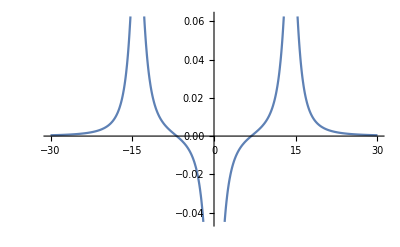

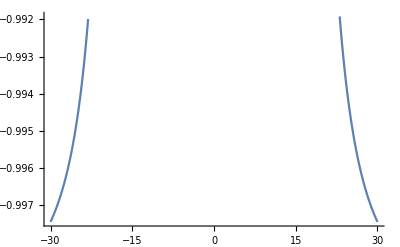

```mathematica
Plot[Im[σ[[2,1]]],{Δp,-30,30}]
Plot[σ[[2,2]]-σ[[1,1]],{Δp,-30,30}]
```

## For Plot

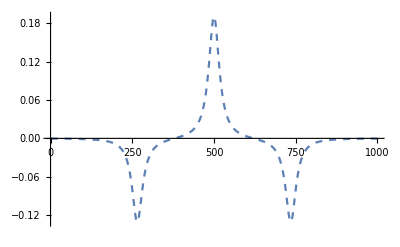

```mathematica
Imax=1000;

For[i=0,i≤Imax,i++,

Δp=-30+i*60/Imax;

γ1=1;
γ2=1;
γp=1;
γc=1;

Δc=0;
Δ1=0;
Δ2=Δp+Δc-Δ1;

Ωc0=10;
Ωp0=0.05;
Ω10=10;
Ω20=1;

ϕ=π;

S=Solve[{
(* 1 1 *)  γp σ22+γ2 σ44+ⅈ Ω20(σ41-σ14)+ⅈ Ωp0( σ21-σ12)==0, 1/2 (-2 ⅈ σ11* Ωp0+2 ⅈ σ22 *Ωp0-γp *σ12+2 ⅈ Δp *σ12+2 ⅈ ⅇ^(-ⅈ ϕ) Ω20 *σ42-2 ⅈ ⅇ^(-ⅈ ϕ) Ωc0 *σ13)==0,-1/2 ⅈ(2 ⅇ^(ⅈ ϕ) Ωc0* σ12-ⅈ  (γ1+γc-2 ⅈ (Δ1+Δ2)) σ13-2 (ⅇ^(ⅈ ϕ) Ωp0 *σ23+ Ω20 *σ43-Ω10 *σ14))==0,1/2 (-2 ⅈ (σ11 *Ω20-σ44 *Ω20-ⅇ^(ⅈ ϕ) σ24* Ωp0)-2 ⅈ Ω10*σ13-(γ2-2 ⅈ Δ2) *σ14)==0,


1/2 (-2 ⅈ ⅇ^(ⅈ ϕ) (σ24 *Ω20-σ31* Ωc0)- (γp* σ21+2 ⅈ (Δp *σ21+(-σ11+σ22) Ωp0)))==0,
(* 2 2 *) -γp σ22+γc σ33+ⅈ Ωc0(σ32-σ23)+ⅈ Ωp0(σ12-σ21)==0, 
1/2 (-2 ⅈ (σ24 *Ω10+σ22* Ωc0-σ33 *Ωc0)+2 ⅈ ⅇ^(-ⅈ ϕ) Ωp0 *σ13-(γ1+γc+γp-2 ⅈ (Δ1+Δ2-Δp))*σ23)==0,
-(γ2* σ24)/2-(γp *σ24)/2+ⅈ Δ2 *σ24-ⅈ Δp *σ24-ⅈ ⅇ^(-ⅈ ϕ) σ21* Ω20+ⅈ σ34 *Ωc0-ⅈ Ω10 *σ23+ⅈ ⅇ^(-ⅈ ϕ) Ωp0 *σ14==0,

 1/2  (- (γ1 *σ31+γc* σ31+2 ⅈ (Δ1 *σ31+Δ2 *σ31-σ41 *Ω10+σ34 *Ω20))+2 ⅈ ⅇ^(ⅈ ϕ) (σ21 *Ωc0-σ32 *Ωp0))==0,
(* 3 2 *) - (1/2(γ1+γc+γp)+ⅈ Δc)σ32- ⅈ Ωc0(σ33-σ22)-ⅈ ⅇ^(ⅈ ϕ) σ31 Ωp0+ⅈ Ω10 σ42==0, 
(* 3 3 *) -γ1 σ33-γc σ33+ⅈ Ωc0(σ23-σ32)+ⅈ Ω10(σ43-σ34)==0, 
-1/2  (γ1 *σ34+γ2* σ34+γc* σ34+2 ⅈ Δ1 *σ34+2 ⅈ σ33* Ω10-2 ⅈ σ44 *Ω10+2 ⅈ σ31 *Ω20-2 ⅈ σ24 *Ωc0)==0,

 (* 4 1 *)- (1/2 γ2+ⅈ Δ2)σ41-ⅈ Ω20(σ44-σ11)+ⅈ Ω10 σ31- Ωp0 ⅈ ⅇ^(-ⅈ ϕ)σ42==0,
-1/2 ⅈ  (-2  σ32* Ω10+2 ⅇ^(ⅈ ϕ) σ41 *Ωp0-2 ⅇ^(ⅈ ϕ) Ω20 *σ12-ⅈ  (γ2+γp+2 ⅈ (Δ2-Δp))σ42+2  Ωc0 *σ43)==0,
1/2 ⅈ (2 σ33 *Ω10-2 σ44* Ω10-2 Ωc0 *σ42+2 Ω20 *σ13+ⅈ γ1 *σ43+ⅈ γ2*σ43+ⅈ γc *σ43+2 Δ1*σ43)==0,
(* 4 4 *) γ1 σ33-γ2 σ44+ⅈ Ω10(σ34-σ43)+ⅈ Ω20(σ14-σ41)==0, 

σ11+σ22+σ33+σ44==1

},{σ11,σ12,σ13,σ14,σ21,σ22,σ23,σ24,σ31,σ32,σ33,σ34,σ41,σ42,σ43,σ44}][[1]];

b[i]=S[[5,2]];

]


p2=ListLinePlot[Table[{n,Im[b[n]]},{n,Imax}],PlotRange->All,PlotStyle->Dashed]
```

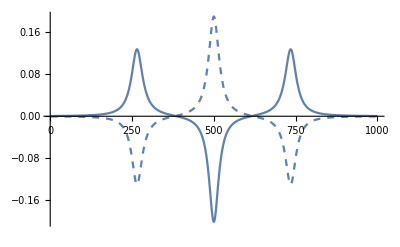

```mathematica
Show[p1,p2,PlotRange->All]
```